```mathematica
influenzaalpha = 2.321995;
influenzabeta = 0.7256236;
influenzaR0=2;
omicronalpha = 2.39;
omicronbeta = 0.3389831;
omicronR0=6;
measlesalpha = 11.35802;
measlesbeta = 0.930985;
measlesR0=12;
```

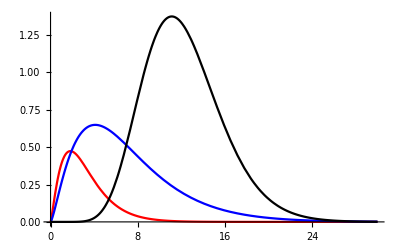

```mathematica
Plot[{
influenzaR0*PDF[GammaDistribution[influenzaalpha, 1/influenzabeta],x],
omicronR0*PDF[GammaDistribution[omicronalpha, 1/omicronbeta],x],
measlesR0*PDF[GammaDistribution[measlesalpha, 1/measlesbeta],x]
},
{x,0,30}, PlotStyle->{Red, Blue, Black}]
```